```mathematica
Deltak=investment-depreciation
```

-depreciation+investment

```mathematica
investmentA=.1;
investmentB=.3;
k=1
```

1

```mathematica
datacap=Table[investmentA-n*0.2*(1-(investmentA-n*0.2)),{n,1,20}]
```

{-0.12,-0.42,-0.8,-1.26,-1.8,-2.42,-3.12,-3.9,-4.76,-5.7,-6.72,-7.82,-9.,-10.26,-11.6,-13.02,-14.52,-16.1,-17.76,-19.5}

```mathematica
dataincome=Table[(1-(investmentA-n*0.2))*0.2,{n,1,20}]
```

{0.22,0.26,0.3,0.34,0.38,0.42,0.46,0.5,0.54,0.58,0.62,0.66,0.7,0.74,0.78,0.82,0.86,0.9,0.94,0.98}

```mathematica
Grid[{datacap, dataincome},Alignment->Left,Frame->All,ItemStyle->"Number",Background->{LightGray,None}]
```

-0.12 | -0.42 | -0.8 | -1.26 | -1.8 | -2.42 | -3.12 | -3.9 | -4.76 | -5.7 | -6.72 | -7.82 | -9. | -10.26 | -11.6 | -13.02 | -14.52 | -16.1 | -17.76 | -19.5
0.22 | 0.26 | 0.3 | 0.34 | 0.38 | 0.42 | 0.46 | 0.5 | 0.54 | 0.58 | 0.62 | 0.66 | 0.7 | 0.74 | 0.78 | 0.82 | 0.86 | 0.9 | 0.94 | 0.98

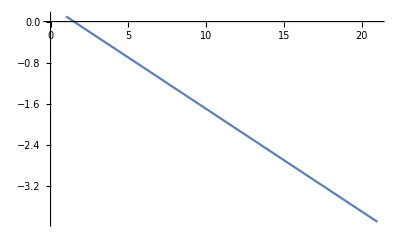

```mathematica
ListLinePlot[dataA]
```

## Problem 3 c and d

```mathematica
dep=0.15;
datacapital=Table[((10*n)/dep)^(5/3),{n,0,3}];
dataoutput=Table[((10*n)/dep)^(2/3),{n,0,3}];
dataconsumption=Table[(1-10*n)((10*n)/dep)^(2/3),{n,0,3}];
mpk=Table[2/5*(((10*n)/dep)^(5/3))^(-3/5)-dep*((10*n)/dep)^(5/3),{n,0,3}];
```

Power::infy: Infinite expression 1/0.^(3/5) encountered.

```mathematica
table=TableForm[{{datacapital,dataoutput,dataconsumption,mpk}},TableHeadings->{{"Saving 0, 10, 20, 30"},{"Capital","Output","Consumption","MPK"}}]
```

| Capital | Output | Consumption | MPK
Saving 0, 10, 20, 30 | 0.
1096.09
3479.88
6839.9 | 0.
16.4414
26.0991
34.1995 | 0.
-147.973
-495.883
-991.786 | ComplexInfinity
-164.408
-521.979
-1025.98

The minimum savings rate maximizes consumption whereas the maximum savings rate maximizes output. Steady-state consumption and marginal product of capital have a directly proportional relationship. As one goes down, so does the other.